```mathematica
(*su(3) fastVersion*)
ClearAll["Global`*"];
t=1;
a=1;
nn=150;
dk=2*Pi/a/nn;
nOfcell=nn*nn;(*num of cells*)
Table[Λ[i,1]=ArrayFlatten@{{PauliMatrix[i],0,0},{0,0PauliMatrix[i],0},{0,0,0PauliMatrix[i]}}; ,{i,1,3}];(*site A*)
Table[Λ[i,2]=ArrayFlatten@{{0 PauliMatrix[i],0,0},{0,PauliMatrix[i],0},{0,0,0PauliMatrix[i]}}; ,{i,1,3}];(*site B*)
Table[Λ[i,3]=ArrayFlatten@{{0 PauliMatrix[i],0,0},{0,0PauliMatrix[i],0},{0,0,PauliMatrix[i]}}; ,{i,1,8}];(*site C*)
sumVec={1,1,1,0,0,0};
GVec={PauliMatrix[1],PauliMatrix[2],PauliMatrix[3]};
mag = N[Table[RandomReal[{-1,1}],{i,1,3},{j,1,3}],4];
mkk[mag0_,U0_]:=
Re@Module[{mag=mag0,U=U0,HkMF,uniMat},
ParallelSum[
HkMF=N[-ArrayFlatten[{
{2 3/4U Dot[mag[[1]],GVec],t Cos[kx a/2]IdentityMatrix[2],t Cos[ky a/2]IdentityMatrix[2]},
{t Cos[kx a/2]IdentityMatrix[2],2 3/4 U Dot[mag[[2]],GVec],0},
{t Cos[ky a/2] IdentityMatrix[2],0,2 3/4U Dot[mag[[3]],GVec]}}],4];
uniMat=(SortBy[Eigensystem@HkMF//Transpose,First]//Transpose)[[2]]//Transpose;
{{Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[1,1],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[2,1],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[3,1],uniMat],sumVec]
},
{Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[1,2],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[2,2],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[3,2],uniMat],sumVec]
},
{Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[1,3],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[2,3],uniMat],sumVec],
Dot[Diagonal@Dot[uniMat//ConjugateTranspose,Λ[3,3],uniMat],sumVec]
}},{kx,0,2Pi/a,dk},{ky,0,2Pi/a,dk}]/nOfcell/2];
```

```mathematica
Do[
mm[U]=FixedPoint[mkk[#,U]&,mag,10];
mag=mm[U];
Print[U],{U,0,5,0.2}]
```

0.

0.2

0.4

0.6

0.8

1.

1.2

1.4

1.6

1.8

2.

2.2

2.4

2.6

2.8

3.

3.2

3.4

3.6

3.8

4.

4.2

4.4

4.6

4.8

5.

```mathematica
N[1/Sqrt[3]]
```

0.57735

```mathematica
Table[Export["/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU2"<>ToString@k<>".eps",ListLinePlot[Table[Table[{i*0.2-0.2,Table[Dot[mm[U],{Normal[SparseArray[k->1,3]]}//Transpose],{U,0,5,0.2}][[i,j,1]]},{i,1,26}],{j,1,3}],PlotRange->All,Frame->True,PlotLabel->k,FrameLabel->{U,S},PlotMarkers->{Automatic, 7},PlotLegends->{1,2,3},AspectRatio->1/2]],{k,1,3}]
```

{/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU21.eps,/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU22.eps,/Users/hanchen/Desktop/毕业设计/SCU_ThesisLatex/SU23.eps}

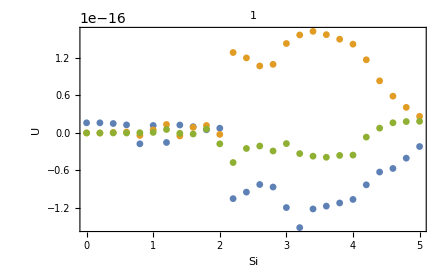
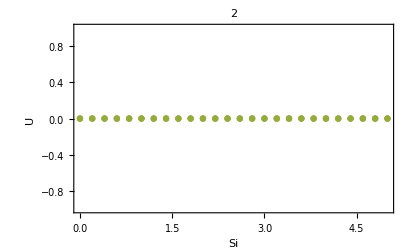
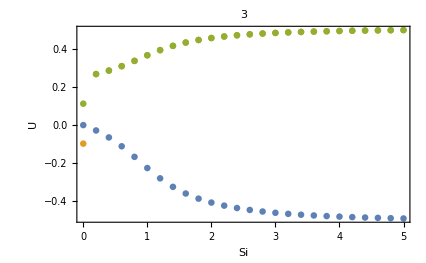

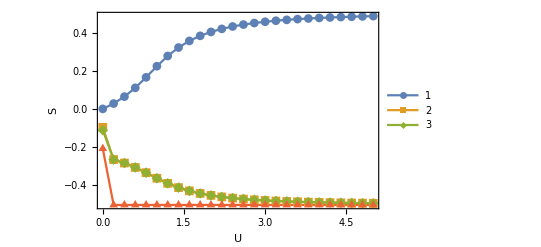

```mathematica
ListLinePlot[{Table[{U,Norm@mm[U][[1]]},{U,0,5,0.2}],-Table[{-U,Norm@mm[U][[2]]},{U,0,5,0.2}],-Table[{-U,Norm@mm[U][[3]]},{U,0,5,0.2}],Table[{U,Norm@mm[U][[1]]},{U,0,5,0.2}]-Table[{0,Norm@mm[U][[2]]},{U,0,5,0.2}]-Table[{0,Norm@mm[U][[3]]},{U,0,5,0.2}]},Frame->True,PlotMarkers->Automatic,PlotLegends->{1,2,3},FrameLabel->{U,S}]
```

```mathematica
Table[{U,Norm@mm[U][[1]]},{U,0,5,0.2}]-Table[{0,Norm@mm[U][[2]]},{U,0,5,0.2}]-Table[{0,Norm@mm[U][[3]]},{U,0,5,0.2}]
```

{{0.,-0.209322},{0.2,-0.506689},{0.4,-0.506689},{0.6,-0.506689},{0.8,-0.506689},{1.,-0.506689},{1.2,-0.506689},{1.4,-0.506689},{1.6,-0.506689},{1.8,-0.506689},{2.,-0.506689},{2.2,-0.506689},{2.4,-0.506689},{2.6,-0.506689},{2.8,-0.506689},{3.,-0.506689},{3.2,-0.506689},{3.4,-0.506689},{3.6,-0.506689},{3.8,-0.506689},{4.,-0.506689},{4.2,-0.506689},{4.4,-0.506689},{4.6,-0.506689},{4.8,-0.506689},{5.,-0.506689}}

```mathematica
Quit[]
```

```mathematica
mkk[mag,1]//AbsoluteTiming
```

{4.7967,{{-0.135988,-0.283624,0.35807},{0.00339944,-0.480276,-0.0892198},{0.208112,-0.441411,0.00068163}}}

```mathematica
Quit
```